```mathematica
TheSize=5;
```

```mathematica
allGraphs=Association[];
g=Graph[Range[TheSize],{}];
Graph[g,VertexLabels->"Name"]
```

-Graphics-

```mathematica
mat = MatrixFromGraph[g]
```

{{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}}

```mathematica
MatrixForm[mat]
```

(2 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 2)

```mathematica
FileName="d:\\Saved\\complete"<>ToString[TheSize]<>".m";
If[FileExistsQ[FileName],
Print["Loading ... ", FileName];
allGraphs=Get[FileName],
Timing[Monitor[ComputeGraph[mat,32],{globalDepth,Length[allGraphs]}]];
Put[allGraphs,FileName]
];
Length[allGraphs]
```

Loading ... d:\Saved\complete5.m

1895

```mathematica
TableForm[Sort[Map[{VertexCount[allGraphs[#,"graph"]],allGraphs[#,"comp"]}&,Keys[allGraphs]]//Tally],TableDepth->2]
```

{1,Greater} | 1
{2,Greater} | 25
{2,GreaterEqual} | 5
{3,Greater} | 170
{3,GreaterEqual} | 30
{4,Greater} | 560
{4,GreaterEqual} | 80
{5,Equal} | 1
{5,Greater} | 938
{5,GreaterEqual} | 85

```mathematica
allGraphs[alfa1Key,"colofournull"]
```

Missing[KeyAbsent,colofournull]

```mathematica
atomKeys=Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofour"]]]==1&];Length[atomKeys]
```

52

```mathematica
PrimePi[52]
```

15

```mathematica
atomSymbols=Table[allGraphs[k,"colofour"],{k,atomKeys}];Length[atomSymbols]
```

52

```mathematica
TableForm[Map[{VertexCount[allGraphs[#,"graph"]],allGraphs[#,"comp"]}&,atomKeys]//Tally//Sort,TableDepth->2]
```

{1,Greater} | 1
{2,Greater} | 10
{2,GreaterEqual} | 5
{3,Greater} | 10
{3,GreaterEqual} | 15
{4,GreaterEqual} | 10
{5,Equal} | 1

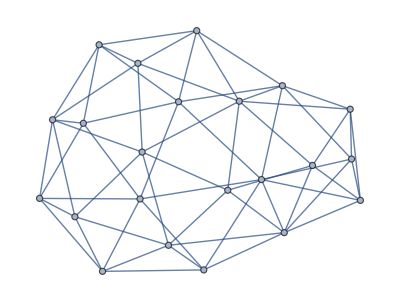

```mathematica
t1=EmbedGraph5[allGraphs,29525]
```

```mathematica
ChromaticPolynomial[t1,x]//Factor
```

(-3+x)^2 (-2+x) (-1+x) x (-3053471859+11713171754 x-21659909324 x^2+25706587375 x^3-21968414035 x^4+14358379086 x^5-7432563569 x^6+3110463439 x^7-1064164349 x^8+298893160 x^9-68806846 x^10+12887070 x^11-1936556 x^12+228240 x^13-20346 x^14+1291 x^15-52 x^16+x^17)

```mathematica
Factor[-54962493462 x+329922494073 x^2-935242750149 x^3+1674618263983 x^4-2134597748296 x^5+2067362360458 x^6-1583866131310 x^7+985673628277 x^8-507201201713 x^9+218337377429 x^10-79182857109 x^11+24271278474 x^12-6287055061 x^13+1371513808 x^14-250218188 x^15+37751766 x^16-4632035 x^17+450839 x^18-33512 x^19+1788 x^20-61 x^21+x^22]/(-6 x+11 x^2-6 x^3+x^4)//Simplify
```

(-3+x) (-3053471859+11713171754 x-21659909324 x^2+25706587375 x^3-21968414035 x^4+14358379086 x^5-7432563569 x^6+3110463439 x^7-1064164349 x^8+298893160 x^9-68806846 x^10+12887070 x^11-1936556 x^12+228240 x^13-20346 x^14+1291 x^15-52 x^16+x^17)

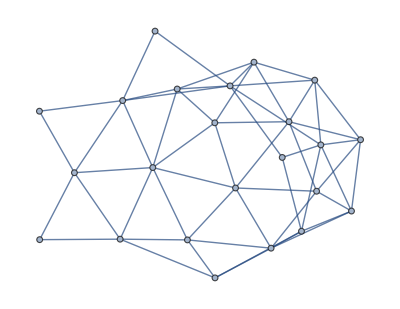

```mathematica
t2=EmbedGraph5[allGraphs,0]
```

```mathematica
ChromaticPolynomial[t2,x]//Factor
```

(-3+x) (-2+x)^4 (-1+x) x (106981430-446200325 x+896155967 x^2-1152218897 x^3+1062232162 x^4-744453004 x^5+409947604 x^6-180685517 x^7+64307559 x^8-18508402 x^9+4285230 x^10-788314 x^11+112768 x^12-12108 x^13+919 x^14-44 x^15+x^16)

```mathematica
Factor[ChromaticPolynomial[t2,x]]/(-6 x+11 x^2-6 x^3+x^4)//Simplify
```

(-2+x)^3 (106981430-446200325 x+896155967 x^2-1152218897 x^3+1062232162 x^4-744453004 x^5+409947604 x^6-180685517 x^7+64307559 x^8-18508402 x^9+4285230 x^10-788314 x^11+112768 x^12-12108 x^13+919 x^14-44 x^15+x^16)

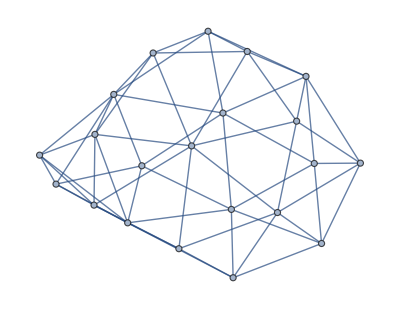

```mathematica
t3=EmbedGraph5[allGraphs,alfa1Key]
```

```mathematica
ChromaticPolynomial[t3,x]//Factor
```

(-3+x) (-2+x) (-1+x) x (-3353740234+13085030629 x-24517961153 x^2+29370871182 x^3-25239183111 x^4+16529493884 x^5-8546741853 x^6+3562821276 x^7-1211268450 x^8+337363171 x^9-76869627 x^10+14226301 x^11-2109224 x^12+244928 x^13-21485 x^14+1340 x^15-53 x^16+x^17)

```mathematica
ChromaticPolynomial[t3,x]/ChromaticPolynomial[allGraphs[alfa1Key,"graph"],x]//Simplify//Factor
```

(-3+x) (-3353740234+13085030629 x-24517961153 x^2+29370871182 x^3-25239183111 x^4+16529493884 x^5-8546741853 x^6+3562821276 x^7-1211268450 x^8+337363171 x^9-76869627 x^10+14226301 x^11-2109224 x^12+244928 x^13-21485 x^14+1340 x^15-53 x^16+x^17)

```mathematica
ChromaticPolynomial[t3,x]/ChromaticPolynomial[t2,x]
```

(20122441404 x-115401326348 x^2+311165545241 x^3-527786723783 x^4+634707479215 x^5-577551165770 x^6+413910853690 x^7-239807234454 x^8+114268589738 x^9-45271801485 x^10+15002644619 x^11-4166371179 x^12+967725588 x^13-186898465 x^14+29704763 x^15-3823167 x^16+388896 x^17-30114 x^18+1669 x^19-59 x^20+x^21)/(5135108640 x-38534644400 x^2+137515527296 x^3-311331909336 x^4+503046209938 x^5-618395475183 x^6+601703972351 x^7-475706645796 x^8+311096464913 x^9-170339452293 x^10+78704243534 x^11-30820309427 x^12+10242749677 x^13-2884626791 x^14+685399961 x^15-136346904 x^16+22444318 x^17-3005254 x^18+319189 x^19-25884 x^20+1506 x^21-56 x^22+x^23)

```mathematica
allGraphs[0,"graph"]
```

-Graphics-

```mathematica
TableForm[Table[{k,allGraphs[k,"graph"],ChromaticPolynomial[allGraphs[k,"graph"],x]//Factor,ChromaticPolynomial[allGraphs[k,"graph"],x],ChromaticPolynomial[allGraphs[k,"graph"],4]},{k,atomKeys}],TableDepth->2]
```

29524 | -Graphics- | (-4+x) (-3+x) (-2+x) (-1+x) x | 24 x-50 x^2+35 x^3-10 x^4+x^5 | 0
29525 | -Graphics- | (-3+x) (-2+x) (-1+x) x | -6 x+11 x^2-6 x^3+x^4 | 24
29527 | -Graphics- | (-3+x) (-2+x) (-1+x) x | -6 x+11 x^2-6 x^3+x^4 | 24
29533 | -Graphics- | (-3+x) (-2+x) (-1+x) x | -6 x+11 x^2-6 x^3+x^4 | 24
29537 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
29551 | -Graphics- | (-3+x) (-2+x) (-1+x) x | -6 x+11 x^2-6 x^3+x^4 | 24
29560 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
29605 | -Graphics- | (-3+x) (-2+x) (-1+x) x | -6 x+11 x^2-6 x^3+x^4 | 24
29608 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
29633 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
29767 | -Graphics- | (-3+x) (-2+x) (-1+x) x | -6 x+11 x^2-6 x^3+x^4 | 24
29768 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
29797 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
29857 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
29888 | -Graphics- | (-1+x) x | -x+x^2 | 12
30253 | -Graphics- | (-3+x) (-2+x) (-1+x) x | -6 x+11 x^2-6 x^3+x^4 | 24
30262 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
30334 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
30496 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
30586 | -Graphics- | (-1+x) x | -x+x^2 | 12
31711 | -Graphics- | (-3+x) (-2+x) (-1+x) x | -6 x+11 x^2-6 x^3+x^4 | 24
31714 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
31738 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
31954 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
31984 | -Graphics- | (-1+x) x | -x+x^2 | 12
32441 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
32684 | -Graphics- | (-1+x) x | -x+x^2 | 12
36085 | -Graphics- | (-3+x) (-2+x) (-1+x) x | -6 x+11 x^2-6 x^3+x^4 | 24
36086 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
36112 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
36166 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
36194 | -Graphics- | (-1+x) x | -x+x^2 | 12
36817 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
36898 | -Graphics- | (-1+x) x | -x+x^2 | 12
38281 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
38308 | -Graphics- | (-1+x) x | -x+x^2 | 12
39014 | -Graphics- | (-1+x) x | -x+x^2 | 12
49207 | -Graphics- | (-3+x) (-2+x) (-1+x) x | -6 x+11 x^2-6 x^3+x^4 | 24
49208 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
49210 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
49216 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
49220 | -Graphics- | (-1+x) x | -x+x^2 | 12
49963 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
49972 | -Graphics- | (-1+x) x | -x+x^2 | 12
51475 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
51478 | -Graphics- | (-1+x) x | -x+x^2 | 12
52232 | -Graphics- | (-1+x) x | -x+x^2 | 12
56011 | -Graphics- | (-2+x) (-1+x) x | 2 x-3 x^2+x^3 | 24
56012 | -Graphics- | (-1+x) x | -x+x^2 | 12
56770 | -Graphics- | (-1+x) x | -x+x^2 | 12
58288 | -Graphics- | (-1+x) x | -x+x^2 | 12
59048 | -Graphics- | x | x | 4

```mathematica
repZero=Sort[Map[allGraphs[#,"colofour"]->0&,Select[Keys[allGraphs],ToString[allGraphs[#,"comp"]]=="Equal"&&Length[DeleteDuplicates[ListofVars[allGraphs[#,"colofour"]]]]==1&]]];Length[repZero]
```

1

```mathematica
repcolofourtextBase2=Table[allGraphs[k,"colofour"]->Style[allGraphs[k,"colofour"],ColourForKey[allGraphs,k]],{k,atomKeys}];
```

```mathematica
Take[repcolofourtextBase2,-20]
```

{v135x2x4→v135x2x4,v135x24→v135x24,v134x2x5→v134x2x5,v134x25→v134x25,v1345x2→v1345x2,v12x3x4x5→v12x3x4x5,v12x3x45→v12x3x45,v12x35x4→v12x35x4,v12x34x5→v12x34x5,v12x345→v12x345,v125x3x4→v125x3x4,v125x34→v125x34,v124x3x5→v124x3x5,v124x35→v124x35,v1245x3→v1245x3,v123x4x5→v123x4x5,v123x45→v123x45,v1235x4→v1235x4,v1234x5→v1234x5,v12345→v12345}

```mathematica
repcolofourgraph2=Table[allGraphs[k,"colofour"]->Framed[Labeled[allGraphs[k,"graph"],{Style[allGraphs[k,"colofour"],Bold],Style[k,ColourForKey[allGraphs,k]]},{Top,Bottom}],FrameStyle->Directive[Blue]],{k,atomKeys}];
```

## Now we look at the polynomials

```mathematica
ChromaticPolynomial[allGraphs[alfa1Key,"graph"],x]//Factor
```

(-2+x) (-1+x) x

```mathematica
repAtoms=Table[allGraphs[k,"colofour"]->Factor[ChromaticPolynomial[allGraphs[k,"graph"],x]*allGraphs[k,"colofour"]],{k,atomKeys}]
```

{v1x2x3x4x5→v1x2x3x4x5 (-4+x) (-3+x) (-2+x) (-1+x) x,v1x2x3x45→v1x2x3x45 (-3+x) (-2+x) (-1+x) x,v1x2x35x4→v1x2x35x4 (-3+x) (-2+x) (-1+x) x,v1x2x34x5→v1x2x34x5 (-3+x) (-2+x) (-1+x) x,v1x2x345→v1x2x345 (-2+x) (-1+x) x,v1x25x3x4→v1x25x3x4 (-3+x) (-2+x) (-1+x) x,v1x25x34→v1x25x34 (-2+x) (-1+x) x,v1x24x3x5→v1x24x3x5 (-3+x) (-2+x) (-1+x) x,v1x24x35→v1x24x35 (-2+x) (-1+x) x,v1x245x3→v1x245x3 (-2+x) (-1+x) x,v1x23x4x5→v1x23x4x5 (-3+x) (-2+x) (-1+x) x,v1x23x45→v1x23x45 (-2+x) (-1+x) x,v1x235x4→v1x235x4 (-2+x) (-1+x) x,v1x234x5→v1x234x5 (-2+x) (-1+x) x,v1x2345→v1x2345 (-1+x) x,v15x2x3x4→v15x2x3x4 (-3+x) (-2+x) (-1+x) x,v15x2x34→v15x2x34 (-2+x) (-1+x) x,v15x24x3→v15x24x3 (-2+x) (-1+x) x,v15x23x4→v15x23x4 (-2+x) (-1+x) x,v15x234→v15x234 (-1+x) x,v14x2x3x5→v14x2x3x5 (-3+x) (-2+x) (-1+x) x,v14x2x35→v14x2x35 (-2+x) (-1+x) x,v14x25x3→v14x25x3 (-2+x) (-1+x) x,v14x23x5→v14x23x5 (-2+x) (-1+x) x,v14x235→v14x235 (-1+x) x,v145x2x3→v145x2x3 (-2+x) (-1+x) x,v145x23→v145x23 (-1+x) x,v13x2x4x5→v13x2x4x5 (-3+x) (-2+x) (-1+x) x,v13x2x45→v13x2x45 (-2+x) (-1+x) x,v13x25x4→v13x25x4 (-2+x) (-1+x) x,v13x24x5→v13x24x5 (-2+x) (-1+x) x,v13x245→v13x245 (-1+x) x,v135x2x4→v135x2x4 (-2+x) (-1+x) x,v135x24→v135x24 (-1+x) x,v134x2x5→v134x2x5 (-2+x) (-1+x) x,v134x25→v134x25 (-1+x) x,v1345x2→v1345x2 (-1+x) x,v12x3x4x5→v12x3x4x5 (-3+x) (-2+x) (-1+x) x,v12x3x45→v12x3x45 (-2+x) (-1+x) x,v12x35x4→v12x35x4 (-2+x) (-1+x) x,v12x34x5→v12x34x5 (-2+x) (-1+x) x,v12x345→v12x345 (-1+x) x,v125x3x4→v125x3x4 (-2+x) (-1+x) x,v125x34→v125x34 (-1+x) x,v124x3x5→v124x3x5 (-2+x) (-1+x) x,v124x35→v124x35 (-1+x) x,v1245x3→v1245x3 (-1+x) x,v123x4x5→v123x4x5 (-2+x) (-1+x) x,v123x45→v123x45 (-1+x) x,v1235x4→v1235x4 (-1+x) x,v1234x5→v1234x5 (-1+x) x,v12345→v12345 x}

```mathematica
repAtoms=Select[repAtoms,!MemberQ[Table[allGraphs[k,"colofour"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}],#[[1]]]&];
```

```mathematica
repAtoms=Join[repAtoms,Table[allGraphs[k,"colofour"]->ChromaticPolynomial[allGraphs[k,"graph"],x]*allGraphs[k,"colofour"](x-3),{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]
```

{v1x2x3x4x5→v1x2x3x4x5 (-4+x) (-3+x) (-2+x) (-1+x) x,v1x2x3x45→v1x2x3x45 (-3+x) (-2+x) (-1+x) x,v1x2x35x4→v1x2x35x4 (-3+x) (-2+x) (-1+x) x,v1x2x34x5→v1x2x34x5 (-3+x) (-2+x) (-1+x) x,v1x2x345→v1x2x345 (-2+x) (-1+x) x,v1x25x3x4→v1x25x3x4 (-3+x) (-2+x) (-1+x) x,v1x25x34→v1x25x34 (-2+x) (-1+x) x,v1x24x3x5→v1x24x3x5 (-3+x) (-2+x) (-1+x) x,v1x245x3→v1x245x3 (-2+x) (-1+x) x,v1x23x4x5→v1x23x4x5 (-3+x) (-2+x) (-1+x) x,v1x23x45→v1x23x45 (-2+x) (-1+x) x,v1x235x4→v1x235x4 (-2+x) (-1+x) x,v1x234x5→v1x234x5 (-2+x) (-1+x) x,v1x2345→v1x2345 (-1+x) x,v15x2x3x4→v15x2x3x4 (-3+x) (-2+x) (-1+x) x,v15x2x34→v15x2x34 (-2+x) (-1+x) x,v15x24x3→v15x24x3 (-2+x) (-1+x) x,v15x23x4→v15x23x4 (-2+x) (-1+x) x,v15x234→v15x234 (-1+x) x,v14x2x3x5→v14x2x3x5 (-3+x) (-2+x) (-1+x) x,v14x23x5→v14x23x5 (-2+x) (-1+x) x,v14x235→v14x235 (-1+x) x,v145x2x3→v145x2x3 (-2+x) (-1+x) x,v145x23→v145x23 (-1+x) x,v13x2x4x5→v13x2x4x5 (-3+x) (-2+x) (-1+x) x,v13x2x45→v13x2x45 (-2+x) (-1+x) x,v13x245→v13x245 (-1+x) x,v135x2x4→v135x2x4 (-2+x) (-1+x) x,v135x24→v135x24 (-1+x) x,v134x2x5→v134x2x5 (-2+x) (-1+x) x,v134x25→v134x25 (-1+x) x,v1345x2→v1345x2 (-1+x) x,v12x3x4x5→v12x3x4x5 (-3+x) (-2+x) (-1+x) x,v12x3x45→v12x3x45 (-2+x) (-1+x) x,v12x35x4→v12x35x4 (-2+x) (-1+x) x,v12x34x5→v12x34x5 (-2+x) (-1+x) x,v12x345→v12x345 (-1+x) x,v125x3x4→v125x3x4 (-2+x) (-1+x) x,v125x34→v125x34 (-1+x) x,v124x3x5→v124x3x5 (-2+x) (-1+x) x,v124x35→v124x35 (-1+x) x,v1245x3→v1245x3 (-1+x) x,v123x4x5→v123x4x5 (-2+x) (-1+x) x,v123x45→v123x45 (-1+x) x,v1235x4→v1235x4 (-1+x) x,v1234x5→v1234x5 (-1+x) x,v12345→v12345 x,v13x24x5→v13x24x5 (-3+x) (2 x-3 x^2+x^3),v14x25x3→v14x25x3 (-3+x) (2 x-3 x^2+x^3),v1x24x35→v1x24x35 (-3+x) (2 x-3 x^2+x^3),v13x25x4→v13x25x4 (-3+x) (2 x-3 x^2+x^3),v14x2x35→v14x2x35 (-3+x) (2 x-3 x^2+x^3)}

```mathematica
allGraphs[lambdaKey,"colofour"]
```

v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5

```mathematica
Select[allGraphs,With[{g=#["graph"]
```

```mathematica
(allGraphs[,"colofour"]/.{v1x2x3x4x5->0}/.repAtoms)/.repcolofourtextBase2//Factor
```

Missing[KeyAbsent,Null]

```mathematica
Simplify[(v13x24x5+v13x25x4-3 v13x2x4x5+x v13x2x4x5+v14x25x3+v14x2x35-3 v14x2x3x5+x v14x2x3x5+v1x24x35-3 v1x24x3x5+x v1x24x3x5-3 v1x25x3x4+x v1x25x3x4-3 v1x2x35x4+x v1x2x35x4)]
```

v13x24x5+v13x25x4-3 v13x2x4x5+v14x25x3+v14x2x35-3 v14x2x3x5+v1x24x35-3 v1x24x3x5-3 v1x25x3x4-3 v1x2x35x4+v13x2x4x5 x+v14x2x3x5 x+v1x24x3x5 x+v1x25x3x4 x+v1x2x35x4 x

```mathematica
PolynomialReduce[(-4 v13x24x5+x v13x24x5-4 v13x25x4+x v13x25x4+v13x2x4x5-4 v14x25x3+x v14x25x3-4 v14x2x35+x v14x2x35+v14x2x3x5-4 v1x24x35+x v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4),{1},{x}]
```

{{-4 v13x24x5-4 v13x25x4+v13x2x4x5-4 v14x25x3-4 v14x2x35+v14x2x3x5-4 v1x24x35+x (v13x24x5+v13x25x4+v14x25x3+v14x2x35+v1x24x35)+v1x24x3x5+v1x25x3x4+v1x2x35x4},0}

```mathematica
(allGraphs[lambdaKey,"colofour"]/.repAtoms)
```

v13x2x4x5 (-3+x) (-2+x) (-1+x) x+v14x2x3x5 (-3+x) (-2+x) (-1+x) x+v1x24x3x5 (-3+x) (-2+x) (-1+x) x+v1x25x3x4 (-3+x) (-2+x) (-1+x) x+v1x2x35x4 (-3+x) (-2+x) (-1+x) x+v1x2x3x4x5 (-4+x) (-3+x) (-2+x) (-1+x) x+v13x24x5 (-3+x) (2 x-3 x^2+x^3)+v13x25x4 (-3+x) (2 x-3 x^2+x^3)+v14x25x3 (-3+x) (2 x-3 x^2+x^3)+v14x2x35 (-3+x) (2 x-3 x^2+x^3)+v1x24x35 (-3+x) (2 x-3 x^2+x^3)

```mathematica
PolynomialReduce[(allGraphs[lambdaKey,"colofour"]/.{v1x2x3x4x5->0}/.repAtoms),{x},{x}]/.repcolofourtextBase2
```

{{-6 v13x24x5-6 v13x25x4-6 v13x2x4x5-6 v14x25x3-6 v14x2x35-6 v14x2x3x5-6 v1x24x35-6 v1x24x3x5-6 v1x25x3x4+x^2 (-6 v13x24x5-6 v13x25x4-6 v13x2x4x5-6 v14x25x3-6 v14x2x35-6 v14x2x3x5-6 v1x24x35-6 v1x24x3x5-6 v1x25x3x4-6 v1x2x35x4)-6 v1x2x35x4+x^3 (v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4)+x (11 v13x24x5+11 v13x25x4+11 v13x2x4x5+11 v14x25x3+11 v14x2x35+11 v14x2x3x5+11 v1x24x35+11 v1x24x3x5+11 v1x25x3x4+11 v1x2x35x4)},0}

```mathematica
Reduce[Discriminant[First[PolynomialReduce[(allGraphs[lambdaKey,"colofour"]/.{v1x2x3x4x5->0}/.repAtoms),{x},{x}]],x]>0]
```

(v13x25x4|v13x2x4x5|v14x25x3|v14x2x35|v14x2x3x5|v1x24x35|v1x24x3x5|v1x25x3x4|v1x2x35x4)∈Reals&&(v13x24x5<-v13x25x4-v13x2x4x5-v14x25x3-v14x2x35-v14x2x3x5-v1x24x35-v1x24x3x5-v1x25x3x4-v1x2x35x4||v13x24x5>-v13x25x4-v13x2x4x5-v14x25x3-v14x2x35-v14x2x3x5-v1x24x35-v1x24x3x5-v1x25x3x4-v1x2x35x4)

```mathematica
2 v13x24x5+2 v13x25x4-6 v13x2x4x5+2 v14x25x3+2 v14x2x35-6 v14x2x3x5+2 v1x24x35-6 v1x24x3x5-6 v1x25x3x4-6 v1x2x35x4+24 v1x2x3x4x5+(-3 v13x24x5-3 v13x25x4+11 v13x2x4x5-3 v14x25x3-3 v14x2x35+11 v14x2x3x5-3 v1x24x35+11 v1x24x3x5+11 v1x25x3x4+11 v1x2x35x4-50 v1x2x3x4x5) x+(v13x24x5+v13x25x4-6 v13x2x4x5+v14x25x3+v14x2x35-6 v14x2x3x5+v1x24x35-6 v1x24x3x5-6 v1x25x3x4-6 v1x2x35x4+35 v1x2x3x4x5) x^2+(v13x2x4x5+v14x2x3x5+v1x24x3x5+v1x25x3x4+v1x2x35x4-10 v1x2x3x4x5) x^3+v1x2x3x4x5 x^4/.x->4//Simplify
```

6 (v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4)

## Now the empty graph base

```mathematica
PartitionToNullSymbol[part_]:=Block[{end},
end=StringRiffle[Map[SetToString[#]&,Sort[part,Min[#1]<Min[#2]&]],"x"];
Symbol["p"<>end]]
```

```mathematica
GenerateNullEquations[assoc_, vertexCount_]:=Block[
{keysWith6Nodes=Select[Keys[assoc],With[{g=assoc[#]["graph"]},VertexCount[g]==vertexCount]&],
allPartitions=SetPartitions[vertexCount]},
Monitor[ 
Table[
With[{key=First[Select[keysWith6Nodes,With[{g=assoc[#]["graph"]},IsPartitionGraph[g,part]]&]]},
PartitionToNullSymbol[part]==allGraphs[key,"colofour"]
],
{part,allPartitions}],part]
]
```

```mathematica
repNullBase=Map[#[[1]]->#[[2]]&,AndToTable[Reduce[GenerateNullEquations[allGraphs,5],Table[allGraphs[k,"colofour"],{k,atomKeys}]]]];
```

```mathematica
Monitor[Table[allGraphs[k,"colofournull"]=Simplify[allGraphs[k,"colofour"]/.repNullBase],{k,Keys[allGraphs]}],k]
```

{p1x2x3x4x5,p12x3x4x5,1/2 (p123x4x5+p12x3x4x5+p13x2x4x5-p1x23x4x5),1/6 (p1234x5+2 p123x4x5+2 p124x3x5-p12x34x5+2 p12x3x4x5+2 p134x2x5-p13x24x5+2 p13x2x4x5-p14x23x5+2 p14x2x3x5-p1x234x5-p1x23x4x5-p1x24x3x5-p1x2x34x5),1887,1/2 (p1x2x345-p1x2x34x5+p1x2x35x4+p1x2x3x45),-p1x2x35x4+p1x2x3x4x5,p1x2x3x45,-p1x2x3x45+p1x2x3x4x5}
 |  |  |  |

```mathematica
nullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofournull"]]]==1&]];Length[nullAtomKeys]
```

52

```mathematica
nullAtomSymbols=Table[allGraphs[k,"colofournull"],{k,nullAtomKeys}]
```

{p1x2x3x4x5,p1x2x3x45,p1x2x35x4,p1x2x34x5,p1x2x345,p1x25x3x4,p1x25x34,p1x24x3x5,p1x24x35,p1x245x3,p1x23x4x5,p1x23x45,p1x235x4,p1x234x5,p1x2345,p15x2x3x4,p15x2x34,p15x24x3,p15x23x4,p15x234,p14x2x3x5,p14x2x35,p14x25x3,p14x23x5,p14x235,p145x2x3,p145x23,p13x2x4x5,p13x2x45,p13x25x4,p13x24x5,p13x245,p135x2x4,p135x24,p134x2x5,p134x25,p1345x2,p12x3x4x5,p12x3x45,p12x35x4,p12x34x5,p12x345,p125x3x4,p125x34,p124x3x5,p124x35,p1245x3,p123x4x5,p123x45,p1235x4,p1234x5,p12345}

```mathematica
repnullcolofourtextBase2=Table[allGraphs[k,"colofournull"]->Style[allGraphs[k,"colofournull"],ColourForKey[allGraphs,k]],{k,nullAtomKeys}];
```

```mathematica
repcolofournullgraph2=Table[allGraphs[k,"colofournull"]->Framed[Labeled[allGraphs[k,"graph"],{Style[allGraphs[k,"colofournull"],Bold],Style[k,ColourForKey[allGraphs,k]]},{Top,Bottom}],FrameStyle->Directive[Red,Dotted,Thick]],{k,nullAtomKeys}]
```

{p1x2x3x4x5→-Graphics-p1x2x3x4x50,p1x2x3x45→-Graphics-p1x2x3x451,p1x2x35x4→-Graphics-p1x2x35x43,p1x2x34x5→-Graphics-p1x2x34x59,p1x2x345→-Graphics-p1x2x34513,p1x25x3x4→-Graphics-p1x25x3x427,p1x25x34→-Graphics-p1x25x3436,p1x24x3x5→-Graphics-p1x24x3x581,p1x24x35→-Graphics-p1x24x3584,p1x245x3→-Graphics-p1x245x3109,p1x23x4x5→-Graphics-p1x23x4x5243,p1x23x45→-Graphics-p1x23x45244,p1x235x4→-Graphics-p1x235x4273,p1x234x5→-Graphics-p1x234x5333,p1x2345→-Graphics-p1x2345364,p15x2x3x4→-Graphics-p15x2x3x4729,p15x2x34→-Graphics-p15x2x34738,p15x24x3→-Graphics-p15x24x3810,p15x23x4→-Graphics-p15x23x4972,p15x234→-Graphics-p15x2341062,p14x2x3x5→-Graphics-p14x2x3x52187,p14x2x35→-Graphics-p14x2x352190,p14x25x3→-Graphics-p14x25x32214,p14x23x5→-Graphics-p14x23x52430,p14x235→-Graphics-p14x2352460,p145x2x3→-Graphics-p145x2x32917,p145x23→-Graphics-p145x233160,p13x2x4x5→-Graphics-p13x2x4x56561,p13x2x45→-Graphics-p13x2x456562,p13x25x4→-Graphics-p13x25x46588,p13x24x5→-Graphics-p13x24x56642,p13x245→-Graphics-p13x2456670,p135x2x4→-Graphics-p135x2x47293,p135x24→-Graphics-p135x247374,p134x2x5→-Graphics-p134x2x58757,p134x25→-Graphics-p134x258784,p1345x2→-Graphics-p1345x29490,p12x3x4x5→-Graphics-p12x3x4x519683,p12x3x45→-Graphics-p12x3x4519684,p12x35x4→-Graphics-p12x35x419686,p12x34x5→-Graphics-p12x34x519692,p12x345→-Graphics-p12x34519696,p125x3x4→-Graphics-p125x3x420439,p125x34→-Graphics-p125x3420448,p124x3x5→-Graphics-p124x3x521951,p124x35→-Graphics-p124x3521954,p1245x3→-Graphics-p1245x322708,p123x4x5→-Graphics-p123x4x526487,p123x45→-Graphics-p123x4526488,p1235x4→-Graphics-p1235x427246,p1234x5→-Graphics-p1234x528764,p12345→-Graphics-p1234529524}

## Playing with the empty graph base

```mathematica
DeleteDuplicates[Flatten[Table[ListofVars[allGraphs[k,"colofournull"]],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]]//Length
```

51

```mathematica
(Total[Table[allGraphs[k,"colofournull"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]//Simplify)/.repnullcolofourtextBase2
```

1/12 (5 p12345-3 p1234x5-3 p1235x4-5 p123x45+6 p123x4x5-3 p1245x3+7 p124x35-6 p124x3x5-5 p125x34+6 p125x3x4-5 p12x345+8 p12x34x5-4 p12x35x4+8 p12x3x45-6 p12x3x4x5-3 p1345x2+7 p134x25-6 p134x2x5+7 p135x24-6 p135x2x4+7 p13x245-4 p13x24x5-4 p13x25x4-4 p13x2x45+6 p13x2x4x5-5 p145x23+6 p145x2x3+7 p14x235-4 p14x23x5-4 p14x25x3-4 p14x2x35+6 p14x2x3x5-5 p15x234+8 p15x23x4-4 p15x24x3+8 p15x2x34-6 p15x2x3x4-3 p1x2345+6 p1x234x5-6 p1x235x4+8 p1x23x45-6 p1x23x4x5-6 p1x245x3-4 p1x24x35+6 p1x24x3x5-4 p1x25x34+6 p1x25x3x4+6 p1x2x345-6 p1x2x34x5+6 p1x2x35x4-6 p1x2x3x45)

```mathematica
(Total[Table[allGraphs[k,"colofournull"],{k,{36085,31711,29605,29551,29527}}]]//Simplify)/.repnullcolofourtextBase2
```

1/4 (-5 p12345+p1234x5+p1235x4+3 p123x45-2 p123x4x5+p1245x3-3 p124x35+2 p124x3x5+3 p125x34-2 p125x3x4+3 p12x345-2 p12x34x5-2 p12x3x45+2 p12x3x4x5+p1345x2-3 p134x25+2 p134x2x5-3 p135x24+2 p135x2x4-3 p13x245+2 p13x24x5+2 p13x25x4-2 p13x2x4x5+3 p145x23-2 p145x2x3-3 p14x235+2 p14x25x3+2 p14x2x35-2 p14x2x3x5+3 p15x234-2 p15x23x4-2 p15x2x34+2 p15x2x3x4+p1x2345-2 p1x234x5+2 p1x235x4-2 p1x23x45+2 p1x23x4x5+2 p1x245x3+2 p1x24x35-2 p1x24x3x5-2 p1x25x3x4-2 p1x2x345+2 p1x2x34x5-2 p1x2x35x4+2 p1x2x3x45)

```mathematica
allGraphs[lambdaKey,"colofournull"]/.repnullcolofourtextBase2
```

1/6 (p12345+2 p123x45-p124x35+2 p125x34+2 p12x345+p12x34x5-2 p12x35x4+p12x3x45-p134x25-p135x24-p13x245+p13x24x5+p13x25x4-2 p13x2x45+2 p145x23-p14x235-2 p14x23x5+p14x25x3+p14x2x35+2 p15x234+p15x23x4-2 p15x24x3+p15x2x34+p1x23x45+p1x24x35-2 p1x25x34)

```mathematica
Length[Intersection[Simplify[allGraphs[alfa1Key,"colofournull"]==0]//ListofVars,Simplify[allGraphs[36085,"colofournull"]==0]//ListofVars]]
```

34

```mathematica
Simplify[allGraphs[lambdaKey,"colofournull"]==0]/.repcolofournullgraph2
```

-Graphics-p12x34x519692+-Graphics-p12x3x4519684+-Graphics-p13x24x56642+-Graphics-p13x25x46588+-Graphics-p14x25x32214+-Graphics-p14x2x352190+-Graphics-p15x23x4972+-Graphics-p15x2x34738+-Graphics-p1x23x45244+-Graphics-p1x24x3584+2 -Graphics-p123x4526488+2 -Graphics-p125x3420448+2 -Graphics-p12x34519696+2 -Graphics-p145x233160+2 -Graphics-p15x2341062+-Graphics-p1234529524==2 -Graphics-p12x35x419686+2 -Graphics-p13x2x456562+2 -Graphics-p14x23x52430+2 -Graphics-p15x24x3810+2 -Graphics-p1x25x3436+-Graphics-p124x3521954+-Graphics-p134x258784+-Graphics-p135x247374+-Graphics-p13x2456670+-Graphics-p14x2352460

## Inequalities de

```mathematica
ineqsnull=Table[allGraphs[k,"comp"][allGraphs[k,"colofournull"],0],{k,Keys[allGraphs]}];
```

```mathematica
baseZero=Table[allGraphs[k,"colofournull"]==0,{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}];
```

```mathematica
nullAtomFacts=Table[allGraphs[k]["comp"][allGraphs[k]["colofournull"],0],{k,nullAtomKeys}];Length[nullAtomFacts]
```

52

```mathematica
ineqs=Table[allGraphs[k,"comp"][allGraphs[k,"colofour"],0],{k,Keys[allGraphs]}];
```

```mathematica
atomFacts=Table[allGraphs[k]["comp"][allGraphs[k]["colofour"],0],{k,atomKeys}];Length[atomFacts]
```

52

```mathematica
links = ineqs=Table[allGraphs[k,"colofour"]==allGraphs[k,"colofournull"],{k,Keys[allGraphs]}];Length[links]
```

1895

```mathematica
countDone=0;MyLeafCount[exp_]:=Block[{},countDone++;StringLength[ToString[exp]]]
```

```mathematica
ineqsnullSimp=Monitor[Simplify[Fold[And,Join[baseZero,ineqsnull,ineqs,links]],Trig->False,ComplexityFunction->MyLeafCount,Assumptions->Join[atomFacts,nullAtomFacts]],countDone];Length[ineqsnullSimp]
```

3722

```mathematica
ExpressionToTable[Select[ineqsnullSimp,1<=Length[#[[1]]]+Length[#[[2]]]≤2&]/.repZero]/.repcolofournullgraph2
```

{}

```mathematica
(Select[AndToTable[ineqsnullSimp],With[{v=ListofVars[#]},8<Length[#[[1]]]+Length[#[[2]]]≤10&&(Length[Intersection[v,nullAtomSymbols]]>0)&&(Length[Intersection[v,atomSymbols]]>0)]&])/.repcolofourgraph2/.repcolofournullgraph2
```

30

```mathematica
TableForm[Tally[Table[With[{v=DeleteDuplicates[ListofVars[ineqsnullSimp[[k]]]]},{Length[ineqsnullSimp[[k,1]]]+Length[ineqsnullSimp[[k,2]]],(Length[Intersection[v,nullAtomSymbols]]),(Length[Intersection[v,atomSymbols]])}],{k,Length[ineqsnullSimp]}]]//Sort, TableDepth->2]
```

{0,2,0} | 50
{3,4,0} | 75
{4,1,4} | 5
{4,4,0} | 75
{5,2,4} | 10
{5,4,7} | 30
{5,4,10} | 30
{5,4,15} | 15
{5,4,19} | 30
{5,4,26} | 30
{5,5,0} | 20
{8,5,3} | 10
{8,8,0} | 60
{9,4,5} | 15
{9,14,0} | 50
{10,5,5} | 10
{10,10,0} | 10
{10,14,0} | 30
{10,15,0} | 5
{10,15,2} | 5
{11,2,10} | 30
{11,8,3} | 30
{11,14,0} | 115
{11,14,7} | 30
{11,14,12} | 60
{12,1,12} | 10
{12,10,2} | 10
{12,14,0} | 10
{12,14,7} | 10
{14,14,0} | 120
{14,14,3} | 25
{14,14,4} | 30
{15,8,7} | 30
{16,1,16} | 10
{16,2,15} | 10
{17,14,3} | 10
{17,14,8} | 30
{21,14,7} | 50
{25,25,0} | 22
{26,1,26} | 15
{26,50,0} | 1
{26,50,1} | 1
{27,50,0} | 3
{27,50,1} | 3
{27,51,0} | 1
{28,14,19} | 20
{28,50,0} | 4
{28,50,1} | 1
{28,51,1} | 1
{29,25,4} | 10
{29,50,0} | 3
{30,30,0} | 30
{30,50,2} | 3
{31,50,2} | 3
{32,50,0} | 3
{33,14,19} | 60
{33,30,3} | 15
{34,50,2} | 3
{35,25,10} | 12
{35,35,0} | 60
{36,1,36} | 10
{36,30,6} | 15
{36,36,0} | 180
{37,35,2} | 60
{37,37,0} | 60
{38,38,0} | 100
{39,36,3} | 30
{39,38,1} | 10
{39,39,0} | 140
{40,38,2} | 30
{40,39,1} | 15
{40,40,0} | 60
{41,36,5} | 30
{41,38,3} | 30
{41,41,0} | 60
{42,36,6} | 60
{43,37,6} | 60
{43,39,4} | 60
{43,40,3} | 60
{44,44,0} | 30
{45,36,9} | 60
{45,44,1} | 10
{46,39,7} | 60
{47,38,9} | 30
{47,44,3} | 20
{50,41,9} | 60
{50,50,0} | 461
{51,1,51} | 1
{51,50,1} | 10
{52,50,2} | 66
{54,50,4} | 30
{55,50,5} | 160
{59,50,9} | 10
{61,50,11} | 60
{64,50,14} | 125

```mathematica
ExpressionToTable[Select[ineqsnullSimp,With[{v=ListofVars[#]},LengthIntersection[v,atomSymbols]>0&&Intersection[v,nullAtomSymbols]>0]&]/.repZero]/.repcolofournullgraph2
```

{}